图和网络

图是用于显示事物之间联系的一种方式，例如，网页是如何连接的，或者人们是如何形成一个社会网络的。

让我们从一个非常简单的图开始，其中 1 连接到 2，2 连接到 3，3 连接到 4。 每个连接都用→(用 -> 来输入)来表示。

一个非常简单的连接图：

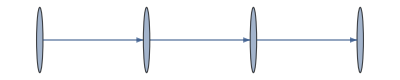

```mathematica
Graph[{1->2,2->3,3->4}]
```

自动标注所有的 “顶点”：

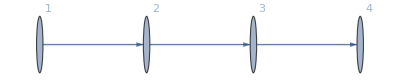

```mathematica
Graph[{1->2,2->3,3->4},VertexLabels->All]
```

让我们再增加一个连接：将 4 连接到 1。现在我们有了一个环。

添加另一个连接，形成一个环：

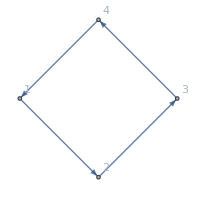

```mathematica
Graph[{1->2,2->3,3->4,4->1},VertexLabels->All]
```

再添加两个连接，包括一个将 2 直接连回到 2。

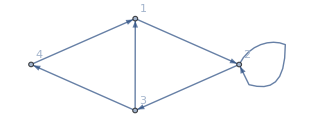

```mathematica
Graph[{1->2,2->3,3->4,4->1,3->1,2->2},VertexLabels->All]
```

当我们添加连接时，Wolfram 语言会选择不同的方式来放置图形的顶点或节点。然而，真正重要的是顶点的连接方式。如果你没有指定，Wolfram 语言会尽量把图铺开，使其尽可能不纠缠，容易理解。

不过，也有一些选项可以指定其他布局。这里有一个例子。这是一个与之前相同的图，有相同的连接，但顶点的布局不同。

同一个图的不同布局(可以通过追踪连接来检查)：

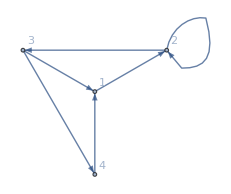

```mathematica
Graph[{1->2,2->3,3->4,4->1,3->1,2->2},VertexLabels->All,GraphLayout-> "RadialDrawing"]
```

你可以在图上做计算，比如说总是沿着箭头走，找到从 4 到 2 的最短路径。

图中从 4 到 2 的最短路径经过 1：

```mathematica
FindShortestPath[Graph[{1->2,2->3,3->4,4->1,3->1,2->2}],4,2]
```

{4,1,2}

现在让我们再做一个图。这一次，我们有 3 个节点，每个节点之间都有一个连接。

首先，使用 3 个对象之间创建一个所有可能连接的数组：

```mathematica
Table[i->j,{i,3},{j,3}]
```

{{1→1,1→2,1→3},{2→1,2→2,2→3},{3→1,3→2,3→3}}

这里的结果是一个列表的列表。但 Graph 需要的只是一个单一的连接列表。我们可以通过使用 Flatten 将子列表“压平”来得到这个结果。

Flatten 将压平所有子列表，无论它们出现在哪里：

```mathematica
Flatten[{{a,b},1,2,3,{x,y,{z}}}]
```

{a,b,1,2,3,x,y,z}

从数组中获得一个压平的连接列表：

```mathematica
Flatten[Table[i->j,{i,3},{j,3}]]
```

{1→1,1→2,1→3,2→1,2→2,2→3,3→1,3→2,3→3}

显示这些连接的图：

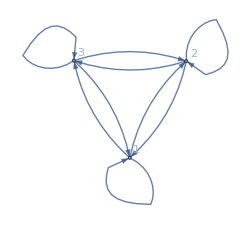

```mathematica
Graph[Flatten[Table[i->j,{i,3},{j,3}]],VertexLabels->All]
```

生成有 6 个节点的完全连接图：

```mathematica
Graph[Flatten[Table[i->j,{i,6},{j,6}]]]
```

-Graphics-

有时连接的“方向”并不重要，所以我们可以舍弃箭头：

该图的“无方向”版本。

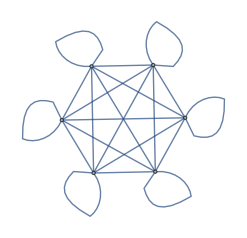

```mathematica
UndirectedGraph[Flatten[Table[i->j,{i,6},{j,6}]]]
```

现在让我们创建一个随机连接的图。下面是一个在随机选择的节点之间有 20 个连接的例子。

在随机选择的编号从 0 到 10 的节点之间创建有 20 个连接的图：

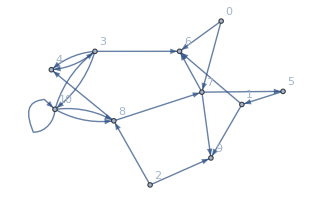

```mathematica
Graph[Table[RandomInteger[10]->RandomInteger[10],20],VertexLabels->All]
```

如果你生成不同的随机数，你会得到不同的图形。这里有 6 张图：

六个随机生成的图：

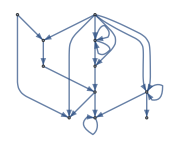
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
Table[Graph[Table[RandomInteger[10]->RandomInteger[10],20]],6]
```

有很多分析可以在图上进行。一个例子是把图分成 “社区”(community)，节点之间的联系比与图的其他部分的联系更多。让我们对一个随机图进行分析。

创建一个将节点的“社区”收集在一起的图：

```mathematica
CommunityGraphPlot[-Graphics-]
```

-Graphics-

其结果是一个与原始连接完全相同的图，但节点的排列说明了该图的“社区结构”。

词汇

Graph[{i→j, ...}] |   | 使用连接来创建图或网络
UndirectedGraph[{i→j, ...}] |   | 无方向连接的图
VertexLabels |   | 要包含什么顶点标签的选项(比如 All)
FindShortestPath[graph,a,b] |   | 查找从一个节点到另一个节点的最短路径
CommunityGraphPlot[list] |   | 按社区结构分布的图
Flatten[list] |   | 将列表中的子列表压平

"共有 11 道习题"
"以及 7 道附加题" | "开始练习 »"

创建一个由 3 个节点组成的循环图。»

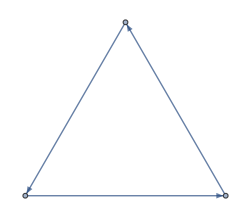
| 期望输出： |  
  | -Graphics- |

创建一个包含 4 个节点的图，其中每个节点都连回到自身并与其它节点互相连接。»

| 期望输出： |  
  | -Graphics- |

创建一个 2 至 10 个节点的无向图的表，其中每个节点都连回到自身并与其它节点相连。»

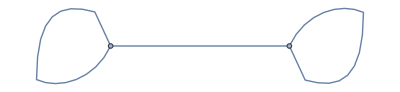
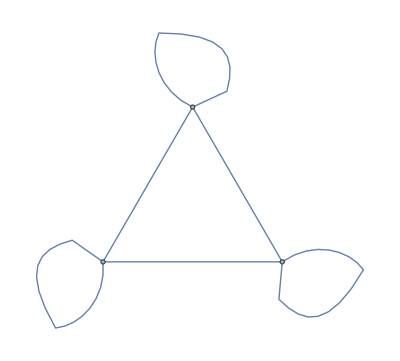
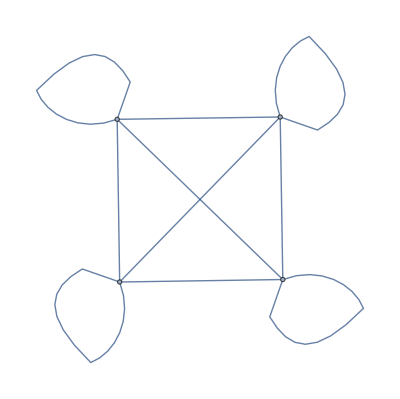
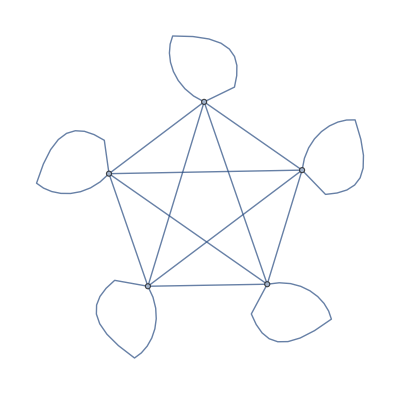
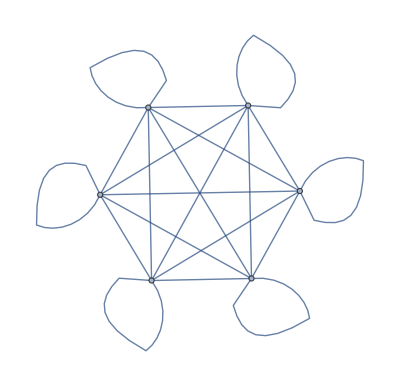
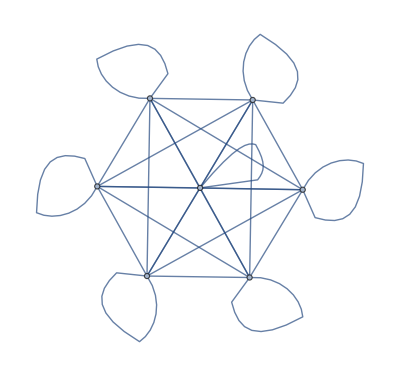
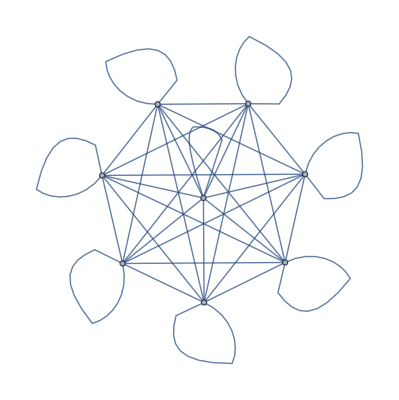
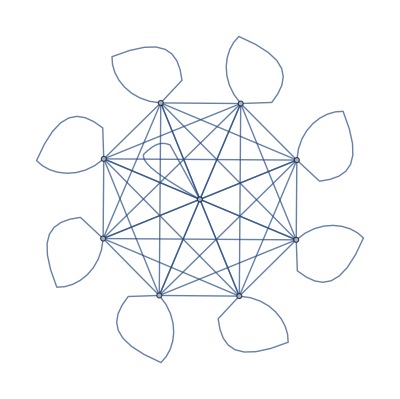
| 期望输出： |  
  | {-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-} |

使用 Table 和 Flatten 来得到 {1,2,1,2,1,2}。»

| 期望输出： |  
  | {1,2,1,2,1,2} |

将从 1 到 100 的数字的各位数连接起来的结果列表(亦即 ...8, 9, 1, 0, 1, 1, 1, 2, ...)创建为线条图。»

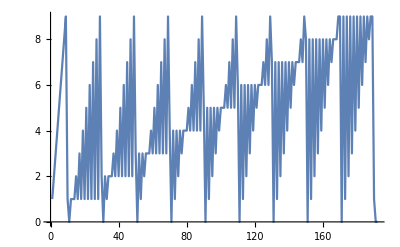
| 期望输出： |  
  | -Graphics- |

创建一个包含 50 个节点的图，其中每个节点 i 都连接到节点 i+1。»

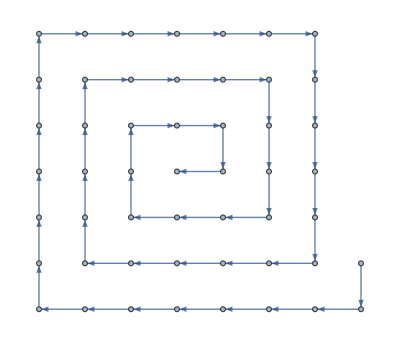
| 期望输出： |  
  | -Graphics- |

创建一个包含 4 个节点的图，其中每个连接都是将 i 连接到 Max[i,j]。»

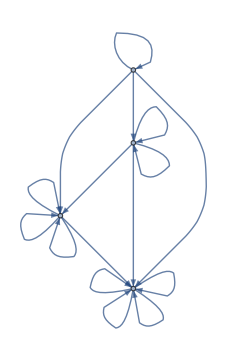
| 期望输出： |  
  | -Graphics- |

创建一个图，其中每个连接都是将 i 连接到 j-i，其中 i 和 j 都是在 1 到 5 之间。»

| 期望输出： |  
  | -Graphics- |

生成一个包含 100 个节点的图，每个节点都连接到一个随机选择的节点。»

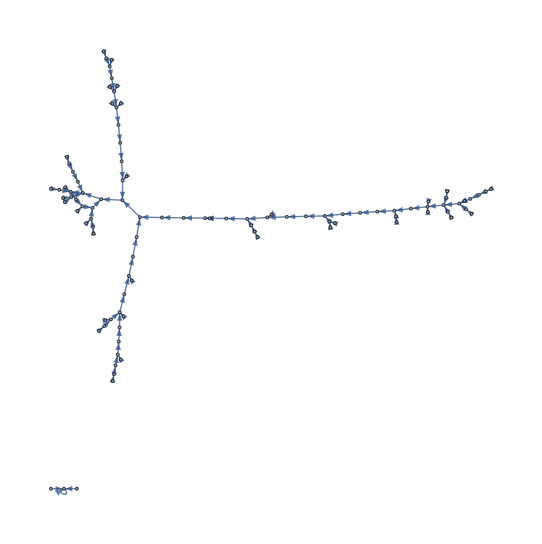
| 期望输出： |  
  | -Graphics- |

生成一个包含 100 个节点的图，每个节点都连接到两个随机选择的节点。»

| 期望输出示例： |  
  | -Graphics- |

对于图 {1→2,2→3,3→4,4→1,3→1,2→2}，创建一个网格，给出每对节点之间的最短路径，以起始节点为行，结束节点为列。»

| 期望输出： |  
  | {1} | {1,2} | {1,2,3} | {1,2,3,4}
{2,3,1} | {2} | {2,3} | {2,3,4}
{3,1} | {3,1,2} | {3} | {3,4}
{4,1} | {4,1,2} | {4,1,2,3} | {4} |

创建一个包含 4 个节点的图，每个节点都连回到自身并与其它节点互相连接，用径向画法显示所得的图。»

| 期望输出： |  
  | -Graphics- |

生成一个图，其中一个节点与其他 10 个节点相连。»

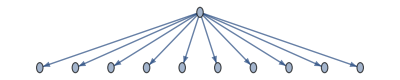
| 期望输出： |  
  | -Graphics- |

使用 Flatten 来生成一个 1 到 50 的数字表，其中偶数的颜色为红色。»

| 期望输出： |  
  | {1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50} |

使用 ImageData、Flatten 和 Totall 来找出 Binarize[Rasterize[“W”]] 中的白色像素的数量。»

| 期望输出： |  
  | 191 |

使用 Flatten、IntegerDigits 和 Total 来计算 1000 以内的所有整数的各位数之和。»

| 期望输出： |  
  | 13501 |

生成一个包含 200 个连接的图，每个连接都是在 100 以内的随机数之间。»

| 期望输出： |  
  | -Graphics- |

生成一个图来显示随机图中的社区，图中包含 200 个 100 以内的数字之间的随机连接。»

| 期望输出： |  
  | -Graphics- |

问&答

“图”和“网络”之间有什么区别？

没有区别。它们只是同一事物的不同叫法，尽管“图”往往在数学和其他正式领域更常见，而“网络”在更多工程应用领域更常见。

什么是图的顶点和边？

顶点是图的点，或节点；边是连接。由于图形出现在许多不同的地方，因此有许多不同的名称用于描述同一事物。

如何理解 i→j？

它就是 Rule[i,j]。在Wolfram 语言中，规则被用于很多地方，例如为选项提供设置。

我可以计算我的 Facebook 好友图谱吗？

是的。使用 SocialMediaData["Facebook","FriendNetwork"]。但请注意，只有那些已授权的朋友会被包括在内。(详见第 44 节)。

Wolfram 语言能处理多大的图？

它主要受限于你的计算机中的内存量。有几万或几十万个节点的图并不是问题。

我可以指定节点和边的属性吗？

是的。你可以给 Graph 提供节点和边的列表，包括像 Property[node,VertexStyle→Red] 或者 Property[edge, EdgeWeight→20] 这样的对象。你也可以给 Graph 提供整体选项。

技术笔记

图，与字符串、图像、图形等对象一样，是 Wolfram 语言中的第一类对象。

你可以使用 <-> 在图中输入非定向的边，它将显示为 <->。

CompleteGraph[n] 将给出包含 n 个节点的完全连接图。其他种类的特殊图，还有 KaryTree、ButterflyGraph、HypercubeGraph 等。

有很多方法可以创建随机图(随机连接、随机连接数、无尺度(scale-free)网络等)。 RandomGraph[{100,200}] 将创建一个有 100 个节点和 200 条边的随机图。

AdjacencyMatrix[graph] 将给出一个图的邻接矩阵。AdjacencyGraph[matrix] 将从一个邻接矩阵创建一个图。

PlanarGraph[graph] 将尝试在没有任何交叉边的情况下展平一个图。

探索更多

Wolfram 语言中的图与网络指南 »